```mathematica
(***************
This is the 3rd version of script of Enqvist model for A-B nucleation.

The main object is free energy of ϕ, though which Subscript[(A^B), αi]=Subscript[(A^A), αi]+ϕ Subscript[D, αi].

The key difference of this version with the first two version is the magnatic field is
taken into account. Key question: Is there spinnordal dicomposition?
 ***************
author : Quang. Zhang (timohyva@github)
22. May, 2022.
***************)
```

```mathematica
Clear[AA,BB,ΔA,ΔB,ϕDD]
AA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
BB=ΔB/(√3) {{1,0,0},{0,1,0},{0,0,1}};
ϕDD=BB-AA
%//MatrixForm
Print[Style["Tr[ϕDD.ϕDD†]:",Red,16]];
Simplify[Tr[ϕDD.ConjugateTranspose[ϕDD]],Assumptions->{{ΔB,ΔA}∈Reals}]
```

{{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}

(-ΔA/(√2)+ΔB/(√3) | -(ⅈ ΔA)/(√2) | 0
0 | ΔB/(√3) | 0
0 | 0 | ΔB/(√3))

Tr[ϕDD.ϕDD†]:

ΔA^2-√(2/3) ΔA ΔB+ΔB^2

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fα,fαϕ];
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************)
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(**********************************)
Print[Style[" α Aαi Aαi^* term:",Red,16]]
fα=Simplify[α Tr[Aαi.AαiH],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fαϕ=Collect[%,ϕ]
```

α Aαi Aαi^* term:

α ΔA^2+(α (3 ΔA^2-√6 ΔA ΔB+3 ΔB^2) ϕ^2)/(3 ϕ0^2)+(α ϕ (-6 ΔA^2 ϕ0+√6 ΔA ΔB ϕ0))/(3 ϕ0^2)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ1,fβ1ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
(**********************************)
Print[Style[" β1 Aαi^* Aαi^* Aβj Aβj term:",Red,16]];
fβ1=FullSimplify[β1 (Tr[AαiC.AαiH]) (Tr[Aαi.AαiT]),Assumptions->{{β1,ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals, ϕ0>0,Δ>0,ΔA>0,ΔB>0}];
fβ1ϕ=Collect[%,ϕ]
```

β1 Aαi^* Aαi^* Aβj Aβj term:

(β1 ΔB^2 (6 ΔA^2-6 √6 ΔA ΔB+9 ΔB^2) ϕ^4)/(9 ϕ0^4)+(2 β1 ΔA^2 ΔB^2 ϕ^2)/(3 ϕ0^2)+(β1 ΔB^2 ϕ^3 (-12 ΔA^2 ϕ0+6 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ2,fβ2ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β2 Aαi^* Aαi Aβj^* Aβj term:",Red,16]];
fβ2=FullSimplify[β2 (Tr[AαiC.AαiT]) (Tr[AαiC.AαiT]),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ2ϕ=Collect[%,ϕ]
```

β2 Aαi^* Aαi Aβj^* Aβj term:

β2 ΔA^4+(β2 (9 ΔA^4-6 √6 ΔA^3 ΔB+24 ΔA^2 ΔB^2-6 √6 ΔA ΔB^3+9 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β2 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-48 ΔA^2 ΔB^2 ϕ0+6 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β2 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+24 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β2 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ3,fβ3ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β3 Aαi^* Aβi^* Aαj Aβj term:",Red,16]]
fβ3=FullSimplify[β3 Tr[(AαiC.AαiH).((Aαi.AαiT)ᵀ)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ3ϕ=Collect[%,ϕ]
```

β3 Aαi^* Aβi^* Aαj Aβj term:

(β3 ΔB^2 (9 ΔA^2-2 √6 ΔA ΔB+3 ΔB^2) ϕ^4)/(9 ϕ0^4)+(β3 ΔA^2 ΔB^2 ϕ^2)/ϕ0^2+(β3 ΔB^2 ϕ^3 (-18 ΔA^2 ϕ0+2 √6 ΔA ΔB ϕ0))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ4,fβ4ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(*****************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(*****************************************)
Print[Style[" β4 Aαi^* Aβi Aβj^* Aαj term:",Red,16]]
fβ4=FullSimplify[β4 Tr[(AαiC.AαiT).(AαiC.AαiT)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ4ϕ=Collect[fβ4,ϕ]
```

β4 Aαi^* Aβi Aβj^* Aαj term:

β4 ΔA^4+(β4 (9 ΔA^4-6 √6 ΔA^3 ΔB+15 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β4 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-30 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β4 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+15 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β4 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fβ5,fβ5ϕ]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(***************************************)
AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
(***************************************)
Print[Style[" β5 Aαi^* Aβi Aβj Aαj^* term:",Red,16]]
fβ5=FullSimplify[β5 Tr[(AαiC.AαiT).(Aαi.AαiH)],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
fβ5ϕ=Collect[fβ5,ϕ]
```

β5 Aαi^* Aβi Aβj Aαj^* term:

β5 ΔA^4+(β5 (9 ΔA^4-6 √6 ΔA^3 ΔB+9 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4) ϕ^4)/(9 ϕ0^4)+(β5 ϕ^3 (-36 ΔA^4 ϕ0+18 √6 ΔA^3 ΔB ϕ0-18 ΔA^2 ΔB^2 ϕ0+2 √6 ΔA ΔB^3 ϕ0))/(9 ϕ0^4)+(β5 ϕ^2 (54 ΔA^4 ϕ0^2-18 √6 ΔA^3 ΔB ϕ0^2+9 ΔA^2 ΔB^2 ϕ0^2))/(9 ϕ0^4)+(β5 ϕ (-36 ΔA^4 ϕ0^3+6 √6 ΔA^3 ΔB ϕ0^3))/(9 ϕ0^4)

```mathematica
Clear[AαiA,Dαi,Aαi,AαiH,AαiC,AαiT,gH,H,HT,h,θ,κ,ϕ0,ϕ,α,β1,β2,β3,β4,β5,fH2,fH2ϕ,fHA2]
AαiA=ΔA/(√2) {{1,I,0},{0,0,0},{0,0,0}};
(*Dαi=1/(√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)) {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}}; with ϕ^2=ΔA^2-√(2/3) ΔA ΔB+ΔB^2*)
Dαi=1/ϕ0 {{-ΔA/(√2)+ΔB/(√3),-(ⅈ ΔA)/(√2),0},{0,ΔB/(√3),0},{0,0,ΔB/(√3)}};(* ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2)*)
Aαi=AαiA+ϕ Dαi;
(**********************************************************)
(** magnetic field vector H, in unit of Gauss = 10^-4 T **)
(*h = 100.0;*)
(** θ, ϕ are arimathal and in-plane angles **)
(*θ= π/3;κ=π/6;*)
θ=π/2;
(** H field is characrized by modul h and a unit vector **)
H=h {Sin[θ] Cos[κ], Sin[θ] Sin[κ], Cos[θ]}; 
HT={H}ᵀ;
(**********************************************************)
(**********************************************************)
Print[Style["A-phase magnetic energy:",Green,18]];
AαiAH=Simplify[ConjugateTranspose[AαiA],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}];
fHA2=FullSimplify[gH (H.((AαiA.AαiAH).HT)),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}]
(**********************************************************)
(*AαiC=Simplify[Conjugate[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];
AαiT=Simplify[Transpose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB}∈Reals}];*)
AαiH=Simplify[ConjugateTranspose[Aαi],Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}];
(***************************************)
Print[Style[" gH A_αi A_βj^* H_α H_β term:",Red,16]]
fH2=FullSimplify[gH (H.((Aαi.AαiH).HT)),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}];
fH2ϕ=Collect[fH2,ϕ]
```

A-phase magnetic energy:

{gH h^2 ΔA^2 Cos[κ]^2}

gH A_αi A_βj^* H_α H_β term:

{gH h^2 ΔA^2 Cos[κ]^2+(gH h^2 ϕ (-6 ΔA^2 ϕ0 Cos[κ]^2+√6 ΔA ΔB ϕ0 Cos[κ]^2))/(3 ϕ0^2)+(gH h^2 ϕ^2 (3 ΔA^2 Cos[κ]^2-√6 ΔA ΔB Cos[κ]^2+ΔB^2 Cos[κ]^2+ΔB^2 Sin[κ]^2))/(3 ϕ0^2)}

```mathematica
fbulk = FullSimplify[fα+fβ1ϕ+fβ2ϕ+fβ3ϕ+fβ4ϕ+fβ5ϕ-(α ΔA^2+β2 ΔA^4+β4 ΔA^4+β5 ΔA^4),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}]
Print[Style[" **************** ",Green,18]];
fHfield = FullSimplify[Level[fH2ϕ,1][[1]]-(gH h^2 ΔA^2 Cos[κ]^2 Sin[π/2]^2),Assumptions->{{ϕ,ϕ0,Δ,α,ΔA,ΔB,h,θ,κ,gH}∈Reals}]
```

1/(9 ϕ0^4)ϕ (3 (3 β1+3 β2+β3+β4+β5) ΔB^4 ϕ^3-6 √6 (β2+β4+β5) ΔA^3 ΔB (ϕ-ϕ0)^3+9 α ΔB^2 ϕ ϕ0^2+9 (β2+β4+β5) ΔA^4 (ϕ-2 ϕ0) (ϕ^2-2 ϕ ϕ0+2 ϕ0^2)-√6 ΔA ΔB (ϕ-ϕ0) (2 (3 β1+3 β2+β3+β4+β5) ΔB^2 ϕ^2+3 α ϕ0^2)+3 ΔA^2 ((2 β1+8 β2+3 β3+5 β4+3 β5) ΔB^2 ϕ^3-2 (2 β1+8 β2+3 β3+5 β4+3 β5) ΔB^2 ϕ^2 ϕ0+(3 α+(2 β1+8 β2+3 β3+5 β4+3 β5) ΔB^2) ϕ ϕ0^2-6 α ϕ0^3))

****************

(gH h^2 ϕ ((ΔB^2 ϕ+3 ΔA^2 (ϕ-2 ϕ0)+√6 ΔA ΔB (-ϕ+ϕ0)) Cos[κ]^2+ΔB^2 ϕ Sin[κ]^2))/(3 ϕ0^2)

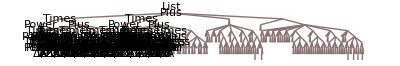

ϕ^4 ((β3 ΔB^2 (9 ΔA^2-2 √6 ΔA ΔB+3 ΔB^2))/(9 ϕ0^4)+(β1 ΔB^2 (6 ΔA^2-6 √6 ΔA ΔB+9 ΔB^2))/(9 ϕ0^4)+(β5 (9 ΔA^4-6 √6 ΔA^3 ΔB+9 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4))/(9 ϕ0^4)+(β4 (9 ΔA^4-6 √6 ΔA^3 ΔB+15 ΔA^2 ΔB^2-2 √6 ΔA ΔB^3+3 ΔB^4))/(9 ϕ0^4)+(β2 (9 ΔA^4-6 √6 ΔA^3 ΔB+24 ΔA^2 ΔB^2-6 √6 ΔA ΔB^3+9 ΔB^4))/(9 ϕ0^4))

```mathematica
fϕ=Collect[(fα+fβ1ϕ+fβ2ϕ+fβ3ϕ+fβ4ϕ+fβ5ϕ+fH2ϕ),ϕ]-(α ΔA^2+β2 ΔA^4+β4 ΔA^4+β5 ΔA^4+gH h^2 ΔA^2 Cos[κ]^2 Sin[π/2]^2);
TreeForm@fϕ
Level[Collect[fϕ,ϕ],2][[1]]
```

```mathematica
Print[Style[" The Simplified f[ϕ] is finally given as: ",18,Blue]]
fϕSimplified=fϕ1Term+fϕ2Term+fϕ3Term+fϕ4Term
```

The Simplified f[ϕ] is finally given as:

fϕ1Term+fϕ2Term+fϕ3Term+fϕ4Term

```mathematica
Clear[α,βwc1,βwc2,βwc3,βwc4,βwc5,βsc1,βsc2,βsc3,βsc4,βsc5,β1,β2,β3,β4,β5,gH,h,κ,θ,βA,βB,ϕ,ϕ0,k,c, J,eV,u,m,m3,ms,s,hz,Gauss,Foa, vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c245,Δ2,ΔA,ΔB];
(*βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);*)
ΔA=(√(-α-gH h^2 Cos[κ]^2 Sin[π/2]^2))/(√2 √(β2+β4+β5))
ΔB=(√(-gH h^2-3 α))/(√2 √(3 β1+3 β2+β3+β4+β5))
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);
FullSimplify[ϕ0,Assumptions->{{α,βA,βB,β1,β2,β3,β4,β5}∈Reals}]
```

(√(-α-gH h^2 Cos[κ]^2))/(√2 √(β2+β4+β5))

(√(-gH h^2-3 α))/(√2 √(3 β1+3 β2+β3+β4+β5))

(√(-(3 (gH h^2+3 α))/(3 β1+3 β2+β3+β4+β5)-(√6 √(-gH h^2-3 α) √(-α-gH h^2 Cos[κ]^2))/(√(β2+β4+β5) √(3 β1+3 β2+β3+β4+β5))-(3 (α+gH h^2 Cos[κ]^2))/(β2+β4+β5)))/(√6)

1.14039×10^51

-0.7775

*******************

-3.42041×10^-31

4.13941×10^40

*******************

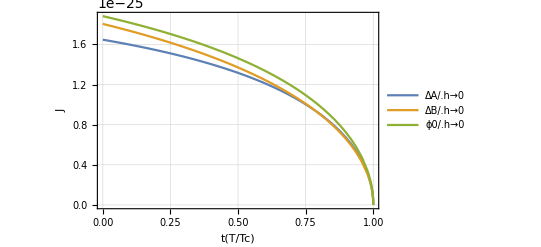

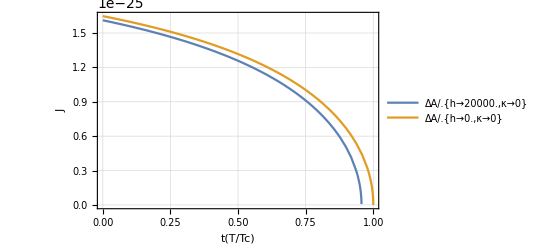

******************

1.39186×10^-25

-6.69452

```mathematica
(*******************************************************************)
(**** take the SC GL model coefficients into the simplified f[ϕ] ***)
(*******************************************************************)
Clear[α,β,βwc1,βwc2,βwc3,βwc4,βwc5,βsc1,βsc2,βsc3,βsc4,βsc5,β1,β2,β3,β4,β5,βA,βB,gH,h,κ,θ,ϕ,ϕ0,k,c, J,eV,u,m,m3,ms,s,hz,Gauss,γ,F0a,vf,kf,Nf,t,T,Tc,kb,c1,c2,c3,c4,c5,c245,Δ2,ΔA,ΔB];
m=1;s=1;J=1;kg=1;k=1;Gauss=1;hz=1/s;
c=2.99792458 10^8 m s^-1;
hbar=1.054571817 10^-34 J s ;(* plank constant *)
kb=1.380649 10^-23 J k^-1;(**J.K^-1*)
(*π=3.1415926;*)
u= 1.66053906660 10^-27 kg ;
m3=3.016293 u;
(**pressure is 32 bar**)
ms=5.66 m3;
Tc=2.463 10^-3 k^-1;(*mK, kevin*)
vf=32.85 m s^-1;
kf=(vf ms)/hbar;
Nf=(ms kf)/(2 π^2 hbar^2)
γ=-3243.409942 hz Gauss^-1;
F0a=−0.7775

c1=-0.0402;c2 = -0.1583;c3=-0.0267;c4=-0.3388;c5=-0.3717;
(**pressure is 4 bar**)
(*ms=3.27 m3;
Tc=1.388 10^-3 k^-1;(*mK, kevin*)
vf=52.36 m s^-1;
kf=(vf ms)/hbar;
Nf=(ms kf)/(2 π^2 hbar^2)
γ=-3243.409942 hz Gauss^-1;
F0a=−0.7392

c1=-0.0155;c2 = -0.0562;c3=-0.0184;c4=-0.0514;c5=-0.1602;*)
(*******  All βi ********)
βwc1=-(7 Nf Zeta[3])/(240 π^2 kb^2 Tc^2);
βwc2=-2 βwc1;βwc3=-2 βwc1;βwc4=-2 βwc1;βwc5=2 βwc1;
βsc1=c1 Abs[βwc1];βsc2=c2 Abs[βwc1];
βsc3=c3 Abs[βwc1];
βsc4=c4 Abs[βwc1];
βsc5=c5 Abs[βwc1];
β1=βwc1+t βsc1;β2=βwc2+t βsc2;
β3=βwc3+t βsc3;
β4=βwc4+t βsc4;
β5=βwc5+t βsc5;
Print[Style["*******************",Red,18]]
γ hbar
gH=5 Abs[βwc1] ((γ hbar)/(1+F0a))^2
(*gH=5 Abs[βwc1]/(1+F0a)^2 (-2.1 10^-30)^2*)
(***** Gap of A and B - phase *****)
Print[Style["*******************",Red,18]]
α=1/3 Nf (t-1);
βA=β2+β4+β5;
βB=β1+β2+1/3 (β3+β4+β5);
ΔA=(√(-α-gH h^2 Cos[κ]^2 Sin[π/2]^2))/(√2 √βA);
ΔB=(√(-gH h^2-3 α))/(√2 √(3 βB));
ϕ0=√(ΔA^2-√(2/3) ΔA ΔB+ΔB^2);
Plot[{ΔA/.h->0,ΔB/.h->0,ϕ0/.h->0},{t,0,1},PlotLegends->"Expressions",AxesLabel->{Style["t(T/Tc)",15],Style["J",15]},Frame->True,GridLines->Automatic,PlotRangePadding->Scaled[.1]]
Plot[{ΔA/.{h->20000.0,κ->0},ΔA/.{h->0.0,κ->0}},{t,0,1},PlotLegends->"Expressions",AxesLabel->{Style["t(T/Tc)",15],Style["J",15]},Frame->True,GridLines->Automatic,PlotRangePadding->Scaled[.1]]

Print[Style[" ****************** ",Green,18]]
ϕ=1.0 ϕ0/.{h->50000,κ->π/2,t->0.5}
(fHfield/fbulk)/.{h->50000,κ->π/2,t->0.5}
```